## Sinus und Kosinus

```mathematica
fs[p_]:=Style[#,FontSize->p]&
sinX[t_, {A_, ω_,φ_}]:=A*Sin[ω*t + φ]
cosX[t_, {A_, ω_,φ_}]:=A*Cos[ω*t + φ]
```

```mathematica
Manipulate[
Plot[
{If[ss==1, sinX[t,{1,1,0}],None], 
If[sc==1, cosX[t, {A,ω,φ}], None]}
,{t, 0, 10}, AxesLabel->fs[14]/@{"t", "x(t)"}, PlotRange->{-6,6}
],
{{A,1,"Amplitude(Betrag)"},0,10},{{ω,1,"Frequenz"},0,3},{{φ,0, "Phase"},-π,π}, 
{{ss,1,"Sinus"},{0,1}},{{sc,1,"Kosinus"},{0,1}}]
```

## Fourier Decomposition

```mathematica
ht[t_]:=If[t==0, 0, HeavisideTheta[t]]
```

```mathematica
signal[t_]:= ht[t-3] -ht[t-6]
fts[t_]=FourierTrigSeries[signal[t],t,10];

ak[t_,k_, f_]:=1/π Integrate[f[t]*Cos[k*t], {t,-π,π}]
bk[t_,k_, f_]:=1/π Integrate[f[t]*Sin[k*t], {t,-π,π}]
```

```mathematica
fourierFunction[t_,kmax_,f_]:=With[{a0= ak[t,0,f]},
akf=ak[t,k,f];
bkf=bk[t,k,f];    
a0/2+Sum[akf*Cos[k*t], {k,1,kmax}] + Sum[bkf*Sin[k*t], {k,1,kmax}]
]
```

```mathematica
fourierFunction[t, 3, signal]
```

(-3+π)/(2 π)-(Cos[t] Sin[3])/π-(Cos[2 t] Sin[6])/(2 π)-(Cos[3 t] Sin[9])/(3 π)+((1+Cos[3]) Sin[t])/π+((-1+Cos[6]) Sin[2 t])/(2 π)+((1+Cos[9]) Sin[3 t])/(3 π)

```mathematica
FourierTrigSeries[signal[t],t,3]
```

1/4 (2-6/π)-(Cos[t] Sin[3])/π-(Cos[2 t] Sin[6])/(2 π)-(Cos[3 t] Sin[9])/(3 π)+((1+Cos[3]) Sin[t])/π-(Sin[3]^2 Sin[2 t])/π+((1+Cos[9]) Sin[3 t])/(3 π)

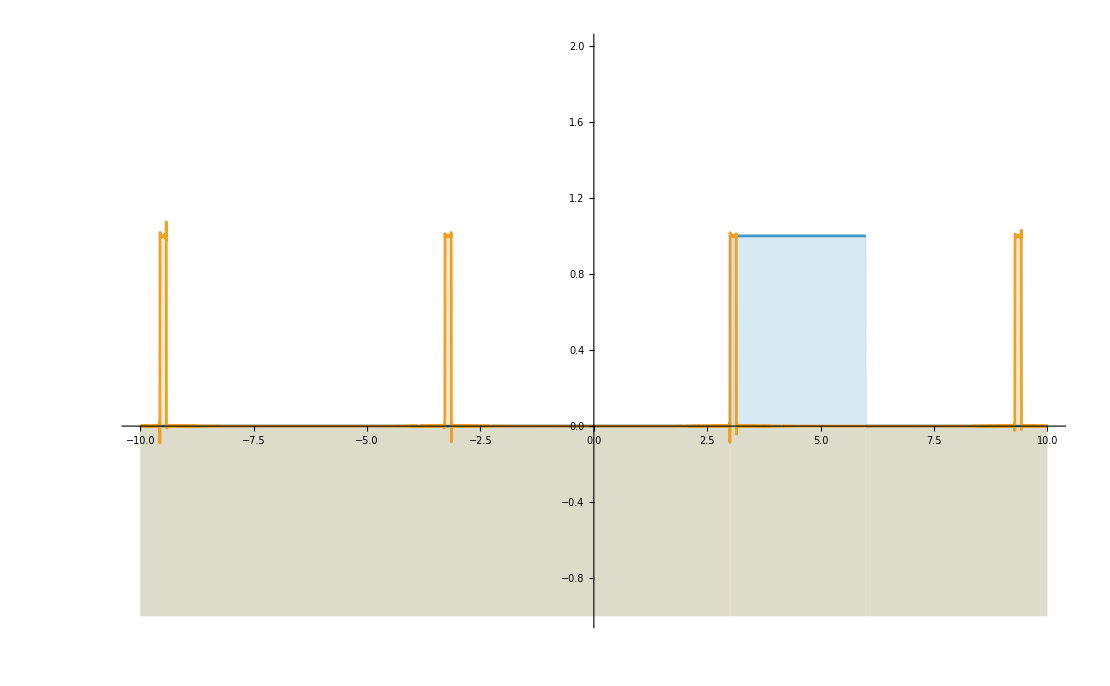

```mathematica
pFunFourier[t_] = fourierFunction[t, 3000, signal];
Plot[{
signal[t], pFunFourier[t]
}, {t, -10,10}, PlotPoints->100,Filling->Bottom, PlotRange->{-1,2}]
```

Die Fourierreihe einer Funktion f(t)  ist definiert als  
f(t) =  a_0/2+ (∑_(k=1))^n a_k*cos(kt) + b_k*sin(kt) 

wobei 
a_k=1/π(∫_-π)^π f(t) cos(kt) ⅆt  

b_k=1/π(∫_-π)^π f(t) sin(kt) ⅆt

```mathematica
ak[t,k, signal]
```

(-Sin[3 k]+Sin[k π])/(k π)

```mathematica
ak[t,k, Sin]
ak[t,k, Cos]
bk[t,k, Sin]
bk[t,k, Cos]
```

0

-(2 k Sin[k π])/((-1+k^2) π)

-(2 Sin[k π])/((-1+k^2) π)

0

1/4 (2-6/π)-(Cos[t] Sin[3])/π-(Cos[2 t] Sin[6])/(2 π)-(Cos[3 t] Sin[9])/(3 π)-(Cos[4 t] Sin[12])/(4 π)-(Cos[5 t] Sin[15])/(5 π)+((1+Cos[3]) Sin[t])/π-(Sin[3]^2 Sin[2 t])/π+((1+Cos[9]) Sin[3 t])/(3 π)-(Sin[6]^2 Sin[4 t])/(2 π)+((1+Cos[15]) Sin[5 t])/(5 π)